```mathematica
polygon[x_]:=
Module[
{list = x},
AppendTo[list,list[[1]]];
Graphics[Line[list]]

];
```

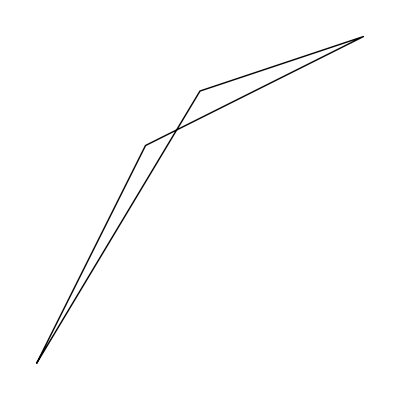

```mathematica
polygon[{{1,0},{4,5},{7,6},{3,4}}]
```